Номер 2
Условие:
а) Вычислить с помощью формулы второго порядка точности и составить таблицу приближенных значений y'_i производной функции f(x) на отрезке [-1, 3] с шагом h = 0,2;
б)  Изобразить на одном чертеже (на отрезке [-1, 3]) график функции f' (x), полученной с помощью функции D пакета Mathematica, и точки (x_i,y'_i) , соответствующие приближенным значениям производной, найденные в пункте а.
a) 
Введем функцию f (x), отрезок и шаг.

```mathematica
f[x_]:=Cot[Sqrt[2*x^2+7]]^2;
a=-1; b=3; h = 0.2;
(*Вычислим количество значений производной на отрезке[-1,3] с шагом h=0,2.*)
n=(b-a)/h;
(*Формула второго порядка точности:*)
pro1 [x_] = (f[x+h]-f[x-h])/(2h);
(*Составим таблицу:*)
Table[{a+h*i,pro1[a+h*i]},{i,0,n}]
```

{{-1.,-913718.},{-0.8,-105.717},{-0.6,-22.675},{-0.4,-8.12805},{-0.2,-2.97026},{0.,0.},{0.2,2.97026},{0.4,8.12805},{0.6,22.675},{0.8,105.717},{1.,913718.},{1.2,-30.5439},{1.4,-913732.},{1.6,-85.2055},{1.8,-16.9023},{2.,-5.96557},{2.2,-2.63473},{2.4,-1.23427},{2.6,-0.463178},{2.8,0.133624},{3.,0.851004}}

б)

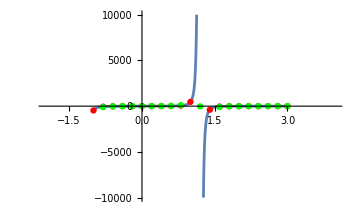

```mathematica
dif[x_]=D[f[x],x];
(*Нарисуем график производной,точки,которые мы высчитали с помощью функции D пакета Mathematica,точки,соответствующие приближенным значениям производной.*)
graphic1 = Plot[dif[x],{x,a,b},PlotRange->{{-2,4}, {-10000, 10000}}];
graphic2 = ListPlot[Table[{a+h*i,dif[a+h*i]},{i,0,n}], PlotStyle->Red];
graphic3 = ListPlot[Table[{a+h*i,pro1[a+h*i]},{i,0,n}], PlotStyle->Green];
Show[graphic1, graphic2, graphic3]
```